```mathematica
Clear[u,a,b,d,S,B,t]
```

```mathematica
B[z_]:=1+2(Sin[π z]/π)^2(1/z-∑_(n=1)^∞ 1/(n+z)^2);
```

```mathematica
S1[d_,b_,z_]:=-1/2(B[d(-b-z)]+B[d(z-b)]);
S2[d_,b_,z_] := 1/2(B[d(b+z)]+B[d(b-z)]);

char[b_,x_] :=If[-b<x<b,1,0];

S1hat[d_, b_, x_] :=  NIntegrate[S1[d, b,t]Cos[2π t x],{t,-200,200}];

S2hat[d_, b_, x_] :=  NIntegrate[S2[d, b,t]Cos[2π t x],{t,-200,200}];

x[n_] := Log[n]/(2π);

id[b_,d_] :=If[S1hat[d,b, x[5]] ≥ 0 ,1.0 , -1.0];

Shat0S1[b_,d_] := 2b - 1/d;

Shat0S2[b_,d_] := 2b + 1/d;

digammaintegralS1[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S1[d,b,r],{r,-200,200}]]-Log[π]Shat0S1[b,d];

digammaintegralS2[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S2[d,b,r],{r,-200,200}]]-Log[π]Shat0S2[b,d];
eta[b_, d_] :=digammaintegralS1[b,d, 0, 0];
```

```mathematica
|
```

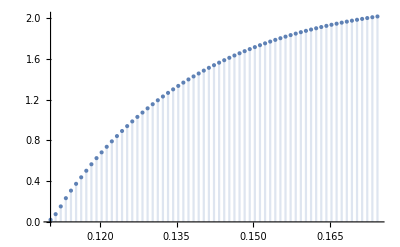

```mathematica
DiscretePlot[S2hat[d,18, x[2]] , {d, x[2], x[3], 0.001}]
```

```mathematica
N[x[2]]
```

0.110318

```mathematica
N[Log[2]]
```

0.693147

```mathematica
N[2Sqrt[2]/Log[2]]
```

4.08056

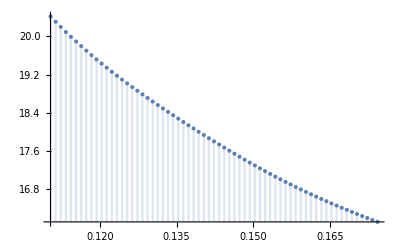

```mathematica
DiscretePlot[digammaintegralS2[21.705,d, 0, 0], {d, x[2], x[3], 0.001}]
```

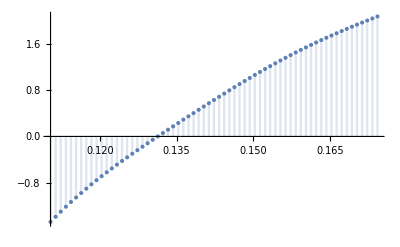

```mathematica
DiscretePlot[digammaintegralS1[21.705,d, 0, 0], {d, x[2], x[3], 0.001}]
```

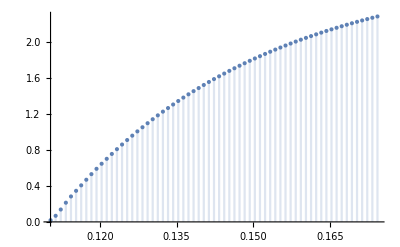

```mathematica
DiscretePlot[S1hat[d, 22, x[2]] , {d, x[2], x[3], 0.001}]
```

```mathematica
Theorem6[mu1_,mu2_,b_,d_] := Sqrt[2]/Log[2] *(digammaintegralS2[b,d, Re[mu1], Im[mu1]] + digammaintegralS2[b,d,  Re[mu2], Im[mu2]] - 1) *S2hat[d,b, x[2]]^(-1);
```

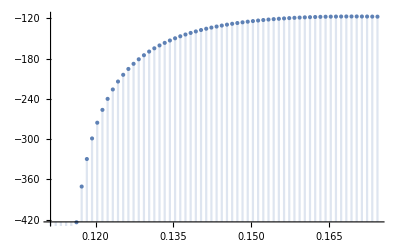

```mathematica
DiscretePlot[Theorem6[0,0,0.5, x[3]], {d, x[2]+0.001, x[3], 0.001}]
```

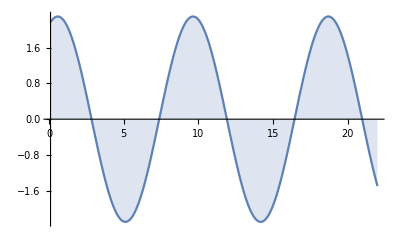

```mathematica
DiscretePlot[S2hat[x[3],b, x[2]] , {b, 0.1,22, 0.1}]
```

```mathematica
S2hat[x[3],0.5, x[2]]
```

2.29099

```mathematica
digammaintegralS2[0.5,x[3], 0,0]
```

-11.9559

```mathematica
Clear[Cor6]
```

```mathematica
Cor6[b_,d_, Q_, degree_] := Sqrt[2]/Log[2] *((2*b + 1/d)Log[Q] + degree/2 *digammaintegralS2[b,d, 0,0] ) *S2hat[d,b, x[2]]^(-1);
```

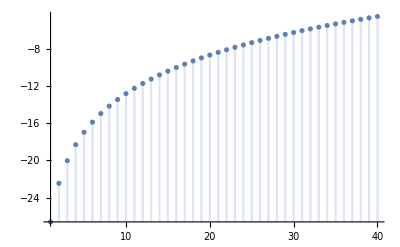

```mathematica
DiscretePlot[Cor6[0.5,x[3], Q,5] , {Q, 1,40, 1}]
```

```mathematica
((2*0.5 + 1/x[3])Log[4] + 1/2 *digammaintegralS2[0.5,x[3], 0,0]) * S2hat[x[3],0.5, x[2]]^(-1)
```

1.4565

```mathematica
S2hat[x[3],0.5, x[2]]
```

2.29099

```mathematica
digammaintegralS2[0.5,x[3], 0,0]
```

-11.9559

```mathematica
num[d_] :=Exp[(-2Log[2]/Sqrt[2]*S2hat[x[3],0.5, x[2]] - d/2 digammaintegralS2[0.5,x[3], 0,0])*(2*0.5 + 1/x[3])^(-1)];
```

```mathematica
num[5]
```

61.2025

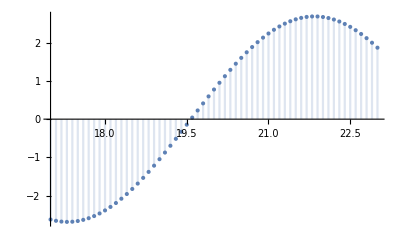

```mathematica
DiscretePlot[S1hat[x[4], b, x[2]], {b, 17,23, 0.1}]
```

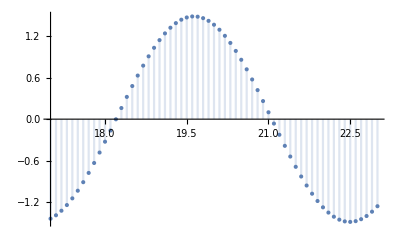

```mathematica
DiscretePlot[S1hat[x[6], b, x[3]], {b, 17,23, 0.1}]
```

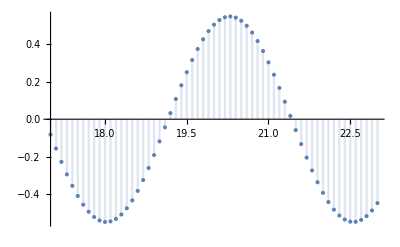

```mathematica
DiscretePlot[S1hat[x[5], b, x[4]], {b, 17,23, 0.1}]
```

```mathematica
Cor7[b_,d_, mu_,nu_] := Sqrt[2]/Log[2] *(1/2 *digammaintegralS2[b,d, 0,mu] + 1/2 *digammaintegralS2[b,d, 0,-mu] + 1/2 *digammaintegralS2[b,d, 0,nu]  + + 1/2 *digammaintegralS2[b,d, 0,-nu] ) *S2hat[d,b, x[2]]^(-1);

IdCor7[mu_,nu_] := If[Cor7[0.5,x[3], mu,nu] < -2 ,-1.0 ,1.0];
```

```mathematica
ListDensityPlot[Table[IdCor7[mu,nu], {mu, 0,20, 1/4},{nu, 0,20, 1/4}], DataRange-> {{0,20},{0,20}}, ColorFunction->GrayLevel]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted